# ACM 11: Project 3 - Topic 1

In this notebook we will investigate a fundamental question in random graph theory: if a graph is generated by some random process, what is the probability that it is connected? We will use Erdős-Rényi Graphs, graphs with n vertices and an edge probability p for all possible edges, as our random graphs and check their connectivity across various n and p.

## Part a

We will first define a makeGraph function that takes in n number of vertices and p edge probability and generate a random Erdős-Rényi graph. This function returns the adjacency matrix of the randomly produced graph.

```mathematica
makeGraph[n_, p_] := AdjacencyMatrix[RandomGraph[BernoulliGraphDistribution[n, p]]]
```

## Part b

Next, we define a connectedProb function that takes in n number of vertices, p edge probability, and m number of graphs to generate. This function will generate m random graphs with n vertices and p edge probability and returns the fraction of graphs which are connected in an effort to estimate the probability that a randomly generated graph with the given parameters in connected.

```mathematica
connectedProb[n_, p_, m_] :=
Module[
(* Local variables *)
{count },

count = 0;

Do [
(* If the randomly generated graph is connected, add it to our numerator *)
count += Boole[ConnectedGraphQ[AdjacencyGraph[makeGraph[n, p]]]],
{m}
];

count / m
]
```

## Part c

Finally, we define various n and p and check the probability that the graph is connected. If it is always connected (connectedProb = 1) we will denote it with a blue dot and if it is never connected 
(connectedProb = 0) we will denote it with a red dot. In order to account for the randomness of the graphs we will allow small error for the connectedProb. The following cell takes ~30sec to run.

```mathematica
ns = PowerRange[50, 2000, 2];
ps = Range[0, .11, .003];
points = Tuples[{ns, ps}];
zeroProb = Table[If[connectedProb[points[[i,1]], points[[i, 2]], 10]≤.1, points[[i]], Unevaluated@Sequence[]],{i,1,Length[points]}];
oneProb = Table[If[connectedProb[points[[i,1]], points[[i, 2]], 10]≥.9, points[[i]], Unevaluated@Sequence[]],{i,1,Length[points]}];
```

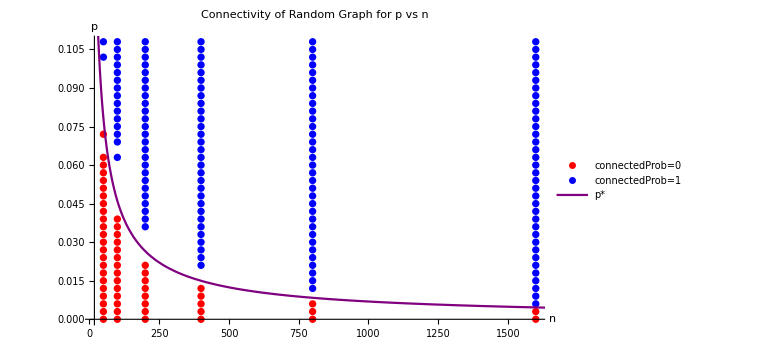

```mathematica
p1= ListPlot[{zeroProb, oneProb}, PlotStyle->{Red, Blue}, PlotRange->All, PlotLegends->{"connectedProb=0", "connectedProb=1"}];
p2 = Plot[ (Log[E, x]/x), {x, 5, 5000}, PlotStyle->{Purple},PlotRange->All, PlotLegends->{"p*"}];
Show[p1, p2, ImageSize->Large, PlotLabel->Style["Connectivity of Random Graph for p vs n", FontSize->18], AxesLabel->{"n", "p"}]
```

From this, we have highlighted the “phase transition” from unconnected to connected regions for various n and p. We clearly see as our n increases the phase transition gets smaller and smaller. We see that we can define a curve p^*=(ln n)/n that divides our connected and unconnected regions. This agrees with the theoretical critical values that have been established with these kind of random graphs. Thus, we can conclude that the probability that a random Erdős-Rényi graph is connected is 1 when the edge probabilities for the graph are larger than p^* and 0 when they are less than p^* for large n.